```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210628_finalising/fxd_bounds"];
```

```mathematica
Get["../../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
stoichioforhomosapiens=Drop[Import["../../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

```mathematica
case="bounds";
intvalues={-1,1};

interval="50perdecobjfuncterms_("<>ToString@intvalues[[1]]<>","<>ToString@intvalues[[2]]<>")";
subsetpositionsforsequences=Import["../cases/subsetpositionsforsequences_half.mx"];
boundaries=Import["../cases/boundaries_for_deleted_reaction_series_-5and5_105.mx"];
boundariespos0=Table[Position[boundaries[[i]],{0,0}],{i,10}];
boundariesposval=Table[Position[boundaries[[i]],{-5,5}],{i,10}];
boundariesa=Table[ReplacePart[(Table[ReplacePart[ConstantArray[{-500,500},fluxexchanges],MapThread[#1->#2&,{boundariespos0[[i]],ConstantArray[{0,0},Length@boundariespos0[[i]]]}]],{i,10}])[[j]],MapThread[#1->#2&,{boundariesposval[[j]],ConstantArray[{-5,5},Length@boundariesposval[[j]]]}]],{j,10}];
```

```mathematica
solutionvectorslist=Import["C:/Users/serha/NonDrive/OR_model-25.06.2021/solution_vectors/"<>interval<>"solutionvectors_fxd"<>case<>"_-5and5_105.mx"];
objfunctionslist=Import["C:/Users/serha/NonDrive/OR_model-25.06.2021/objective_functions/"<>interval<>"objfunc_fxd"<>case<>".mx"];
```

```mathematica
AbsoluteTiming[featuredatalist=Table[MapThread[Dot,{objfunctionslist[[j]],solutionvectorslist[[j]]}],{j,10}];]
```

{1.8194,Null}

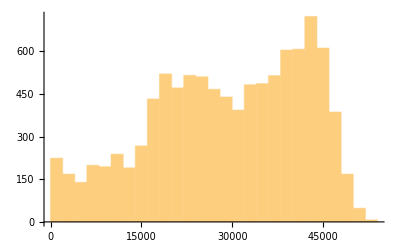
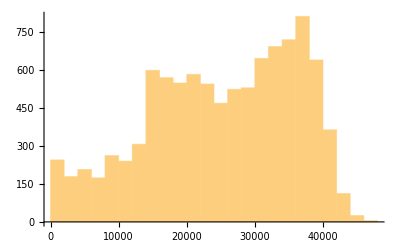
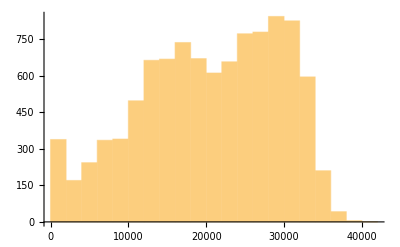
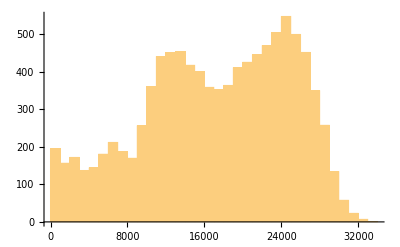
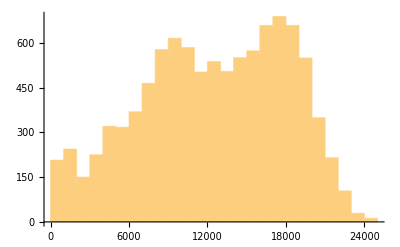
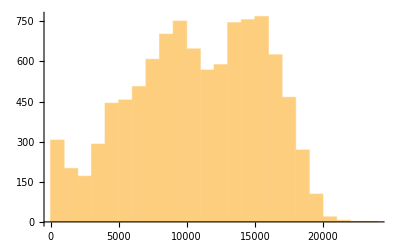
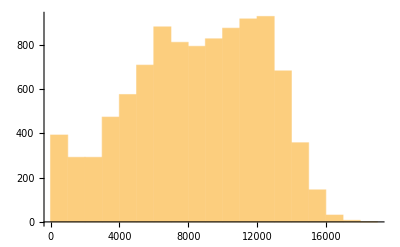
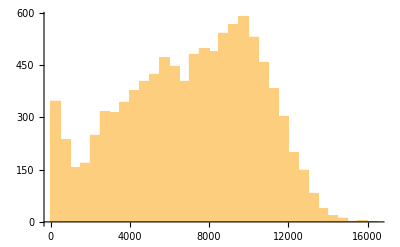

```mathematica
datafulllist=Table[Join[Partition[Range@10000,1],Partition[Flatten@Table[ConstantArray[i,50],{i,200}],1],Partition[featuredatalist[[j]],1],2],{j,10}];
Table[Histogram@datafulllist[[i]][[All,3]],{i,10}]
```

```mathematica
thread={{1,1150},{2,1050},{3,900},{4,800},{5,600},{6,520},{7,425},{8,350},{9,280},{10,210}};
N@Mean@thread[[All,2]]
```

628.5

```mathematica
thread=Thread[{Range@10,2200}]
```

{{1,2200},{2,2200},{3,2200},{4,2200},{5,2200},{6,2200},{7,2200},{8,2200},{9,2200},{10,2200}}

```mathematica
AbsoluteTiming[widthdataFixedstep2=Table[snetworkdatabinned[3,i[[2]],datafulllist[[i[[1]]]]],{i,thread}];]
```

{3.18198,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataFixedstep2[[i]][[1]],widthdataFixedstep2[[i]][[2]],2,7,400,Green],{i,10}];
graphsandnodenumbers12[[All,2]]
```

{25,22,19,16,12,11,9,8,6,5}

```mathematica
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{61.9512,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{25,22,19,16,12,11,9,8,6,5}

ListLinePlot::prng: Value of option PlotRange -> {{0,11},{Indeterminate,Indeterminate}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

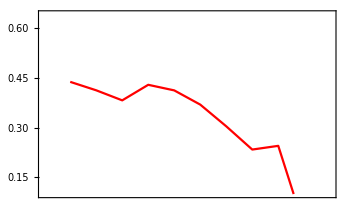
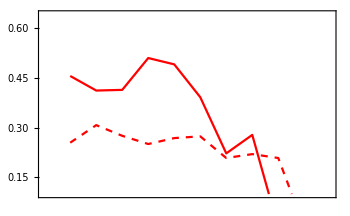
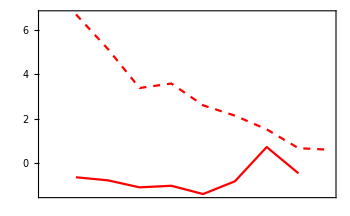

```mathematica
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
AbsoluteTiming[widthdataFixedbucket2=Table[snetworkdatafxdbucket[3,bucketnode12[[i]],datafulllist[[i]]],{i,10}];]
```

{3.21562,Null}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataFixedbucket2[[i]][[1]],widthdataFixedbucket2[[i]][[2]],1.5,7,400,Green],{i,10}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{89.3388,Null}

Power::infy: Infinite expression 1/0. encountered.

{57.5177,Null}

Min::nord: Invalid comparison with ComplexInfinity attempted.

Max::nord: Invalid comparison with ComplexInfinity attempted.

ListLinePlot::prng: Value of option PlotRange -> {{0,11},{-1+Min[-0.505618,ComplexInfinity],1+Max[8.01262,ComplexInfinity]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

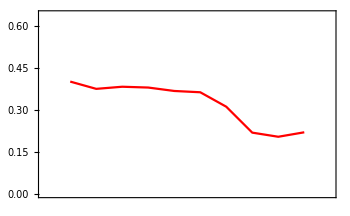
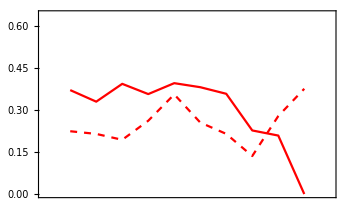
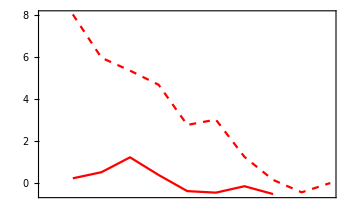

```mathematica
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_-5+5_105-modularityvalues-fss.mx",modularityvalues12]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_-5+5_105-singrand-erd-modularityvalues-fss.mx",singlerandomerdrenmodularityvalues12]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_-5+5_105-singrand-comm-modularityvalues-fss.mx",singlerandomcommmodularityvalues12]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_-5+5_105-zscores-fss.mx",Zscoresmodularity12]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_-5+5_105-modularityvalues-fbs.mx",modularityvalues32]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_-5+5_105-singrand-erd-modularityvalues-fbs.mx",singlerandomerdrenmodularityvalues32]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_-5+5_105-singrand-comm-modularityvalues-fbs.mx",singlerandomcommmodularityvalues32]
Export["plot_values/fxd_"<>case<>"/"<>interval<>"_-5+5_105-zscores-fbs.mx",Zscoresmodularity32]
```

plot_values/fxd_bounds/50perdecobjfuncterms_(-1,1)_-5+5_105-modularityvalues-fss.mx

plot_values/fxd_bounds/50perdecobjfuncterms_(-1,1)_-5+5_105-singrand-erd-modularityvalues-fss.mx

plot_values/fxd_bounds/50perdecobjfuncterms_(-1,1)_-5+5_105-singrand-comm-modularityvalues-fss.mx

plot_values/fxd_bounds/50perdecobjfuncterms_(-1,1)_-5+5_105-zscores-fss.mx

plot_values/fxd_bounds/50perdecobjfuncterms_(-1,1)_-5+5_105-modularityvalues-fbs.mx

plot_values/fxd_bounds/50perdecobjfuncterms_(-1,1)_-5+5_105-singrand-erd-modularityvalues-fbs.mx

plot_values/fxd_bounds/50perdecobjfuncterms_(-1,1)_-5+5_105-singrand-comm-modularityvalues-fbs.mx

plot_values/fxd_bounds/50perdecobjfuncterms_(-1,1)_-5+5_105-zscores-fbs.mx